# helper

```mathematica
getBlack[s_]:=StringCases[s,("B<< Monte-Carlo "~~Shortest[__]~~" total games: "~~(x:DigitCharacter..)~~WordBoundary):>ToExpression[x]/10^6];
getWhite[s_]:=StringCases[s,("W<< Monte-Carlo "~~Shortest[__]~~" total games: "~~(x:DigitCharacter..)~~WordBoundary):>ToExpression[x]/10^6]
```

```mathematica
ClearAll[makePlot];
makePlot[expr_->data_]:=
Module[{all},
all=Join[getBlack[data],getWhite[data]];
all=all;ListLinePlot[{Legended[Style[Take[all,Length[getBlack[data]]],Black],Placed["Black",Below]],Legended[Style[Drop[all,Length[getBlack[data]]],LightGray],Placed["White",Below]]},PlotLabel->StringTrim[expr,"\\"]];
ListLinePlot[{getWhite[data],getBlack[data]},Mesh->All,PlotLabel->Style[StringTrim[expr,"\\"],Medium],PlotRange->All,PlotMarkers->{Automatic,8},ImageSize->Scaled[0.18],PlotStyle->{LightGray,Black}]]
```

```mathematica
?PlotMarkers
```

PlotMarkers is an option for graphics functions like ListPlot and ListLinePlot that specifies what markers to draw at the points plotted.

## OMP

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata=Map[FileNameSplit[#][[2]]->Import[#,"Text"]&,FileNames["OMP*/gtg_output.txt","omp"]];
Length[rawdata]
```

95

```mathematica
data=Normal@Map[Function[{val},StringJoin[Last/@val]],GroupBy[rawdata,StringJoin[Riffle[Most[StringSplit[First[#],"_"]]," "]]&]];
Length[data]
```

10

```mathematica
GraphicsGrid[Partition[makePlot/@Reverse@Sort@Normal[data],5],ImageSize->Scaled[1],ImagePadding->Scaled[0.1]]
```

ListLinePlot::lpn: {{5.44, 5.12, 5.12, 5.28, 5.28, 5.12, 5.12, 5.12, 5.44, 2.72}, {}} is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: {{}, {5.44, 5.12, 5.12, 5.28, 5.28, 5.12, 5.12, 5.12, 5.44, 2.72}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

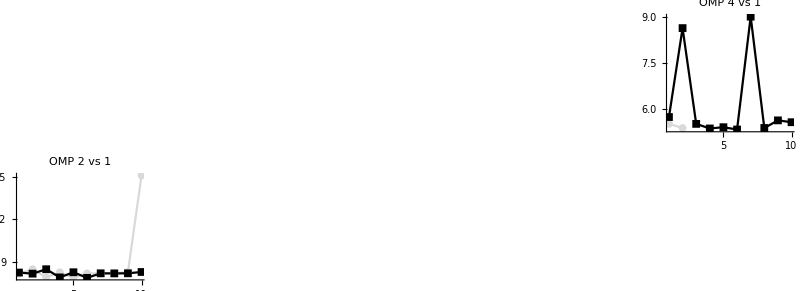

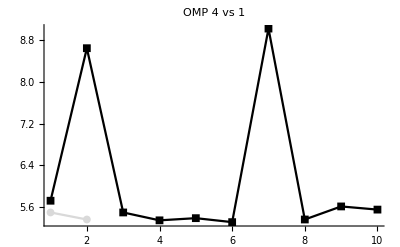
```mathematica
Export[FileNameJoin[{NotebookDirectory[],"stev_1_19_OMP_vs.pdf"}],-Graphics-,ImageSize->Scaled[2],ImagePadding->Scaled[0.4]]
```

C:\Users\adakk\Documents\cs484\data\stev_19_omp\stev_1_19_OMP_vs.pdf

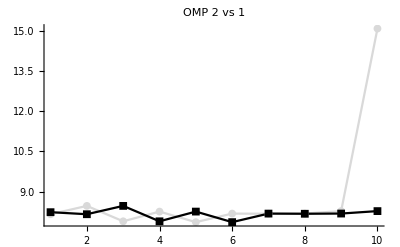
```mathematica
Export[FileNameJoin[{NotebookDirectory[],"stev_2_19_OMP_vs.pdf"}],-Graphics-,ImageSize->Scaled[2],ImagePadding->Scaled[0.4]]
```

C:\Users\adakk\Documents\cs484\data\stev_19_omp\stev_2_19_OMP_vs.pdf